```mathematica
ClearAll["Global`*"]
```

```mathematica
(*G=6.67408*10^-11;*)
G=1;
tmax=20;
```

```mathematica
(* Mass *)
m=Flatten[Import[FileNameJoin[{NotebookDirectory[],  "mass.dat"}]]];
n=Length[m];
M=Sum[m[[i]],{i,n}];
```

```mathematica
(* Initial coord and vel *)
initCoords=Import[FileNameJoin[{NotebookDirectory[], "initpos.dat"}],"Table"];
initVels=Import[FileNameJoin[{NotebookDirectory[], "initvel.dat"}],"Table"];

R=Table[Sum[m[[i]] initCoords[[i,j]]/M,{i,n}],{j,3}];
Rdot=Table[Sum[m[[i]] initVels[[i,j]]/M,{i,n}],{j,3}];
```

```mathematica
(* Initial pos and mom relative to 1 *)
initpositions=Table[initpos[i][j],{i,n-1},{j,3}];
initmoments=Table[initmom[i][j],{i,n-1},{j,3}];

For[i=1,i≤n-1,i++,
For[j=1,j≤3,j++,
initpos[i][j]=initCoords[[1,j]]-initCoords[[i+1,j]];
initmom[i][j]=m[[i+1]](Rdot[[j]]-initVels[[i+1,j]])
]
]
Clear[i,j]
```

```mathematica
(* Defining position and moment variables *)
positions[t_]=Table[pos[i][j][t] ,{i,2,n},{j,3}];
moments[t_]=Table[mom[i][j][t] ,{i,2,n},{j,3}];

For[j=1,j≤3,j++,
pos[1][j][t]=0;
mom[1][j][t]=0
]
Clear[j]
```

```mathematica
(* Potential V *)
Normaij[posi__,i__,j_]:=Sqrt[Sum[(posi[[3( j-2)+k]]-posi[[3(i-2)+k]])^2,{k,3}]]
(*T[velo__]:=1/2(Sum[m[[i]]velo[[i]].velo[[i]],{i,n}])-1/2(Sum[m[[i]]m[[j]]/M velo[[i]].velo[[j]],{i,2,n},{j,2,n}]/M)*)
V[posi__]:=-G Sum[m[[1]]m[[i]]/Sqrt[Sum[posi[[3(i-2)+k]]^2,{k,3}]],{i,2,n}]-G Sum[If[i!=j,m[[i]]m[[j]]/(2*Normaij[posi,i,j]),0],{i,2,n},{j,2,n}]
```

```mathematica
(* Inverse Kinetic Matrix *)
Tmat=Table[If[i==j,m[[i]],0],{i,2,n},{j,2,n}]-Table[m[[i]]m[[j]]/M,{i,2,n},{j,2,n}];
Tmatinv = Inverse[Tmat];
Tmatinvext=Table[If[k==l,Tmatinv[[i,j]],0],{i,n-1},{k,3},{j,n-1},{l,3}];
Tinv = Map[Flatten,Flatten[Tmatinvext,1]];
```

```mathematica
(* Hamiltonean and variables *)
H[posi__,moment__]:=1/2*moment.Tinv.moment + V[posi]
hamiltoneq[1][i_,posi__,moment__,t_]:=( D[H[posi,moment],moment[[i]]]==D[posi[[i]],t])
hamiltoneq[2][i_,posi__,moment__,t_]:=( D[H[posi,moment],posi[[i]]]==-D[moment[[i]],t])

Vec[1][t_] := Flatten[positions[t]]
Vec[2][t_] := Flatten[moments[t]]
H[Vec[1][t],Vec[2][t]];
```

```mathematica
(*  *)
Hamiltoneqs[t_]:= Flatten[Table[hamiltoneq[j][i,Vec[1][t],Vec[2][t],t],{j,2},{i,1,3*(n-1)}]]
initConditions=Table[If[j==1,initpos[i][k]==Vec[1][0][[3*(i-1)+k]],initmom[i][k]==Vec[2][0][[3*(i-1)+k]]],{j,2},{i,n-1},{k,3}];

equations[t_]:=Flatten[{Hamiltoneqs[t],initConditions}]
variables= Flatten[{Table[pos[i][j] ,{i,2,n},{j,3}],Table[mom[i][j] ,{i,2,n},{j,3}]}];
```

```mathematica
(* Solve ODEs *)
solution=Flatten[NDSolve[equations[t],variables,{t,0,tmax},MaxSteps->1000000,PrecisionGoal->20]]
```

{pos[2][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[2][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[2][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[3][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[3][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[3][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[4][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[4][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[4][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[5][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[5][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[5][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[6][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[6][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[6][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[7][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[7][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[7][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[8][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[8][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[8][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[9][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[9][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[9][3]→InterpolatingFunction[{{0., 20.}}, <>],pos[10][1]→InterpolatingFunction[{{0., 20.}}, <>],pos[10][2]→InterpolatingFunction[{{0., 20.}}, <>],pos[10][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[2][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[2][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[2][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[3][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[3][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[3][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[4][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[4][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[4][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[5][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[5][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[5][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[6][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[6][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[6][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[7][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[7][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[7][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[8][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[8][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[8][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[9][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[9][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[9][3]→InterpolatingFunction[{{0., 20.}}, <>],mom[10][1]→InterpolatingFunction[{{0., 20.}}, <>],mom[10][2]→InterpolatingFunction[{{0., 20.}}, <>],mom[10][3]→InterpolatingFunction[{{0., 20.}}, <>]}

```mathematica
(* Ref change to CM *)
For[i=2,i≤n,i++,
For[j=1,j≤3,j++,
pos[i][j] = pos[i][j]/.solution;
mom[i][j] = mom[i][j]/.solution
]
]
Clear[i,j]
```

```mathematica
CentreMass=Table[CM[i],{i,3}];
For[i=1,i≤3,i++,
CM[i][t_]=R[[i]]+Rdot[[i]] t
]
Clear[i]
```

```mathematica
InertialPositions=Table[inerpos[i][j],{i,n},{j,3}];
InertialMoments=Table[inermom[i][j],{i,n},{j,3}];

For[k=1,k≤3,k++,
inerpos[1][k][t_]=Sum[(m[[i]] pos[i][k][t])/M,{i,2,n}]+CM[k][t];
inermom[1][k][t_]=Sum[mom[i][k][t],{i,2,n}]
]
For[i=2,i≤n,i++,
For[j=1,j≤3,j++,
inerpos[i][j][t_]=inerpos[1][j][t]-pos[i][j][t]+CM[j][t];
inermom[i][j][t_]=-mom[i][j][t]
]
]
Clear[k,i,j]
```

```mathematica
(* COOL Plots *)
ParametricPlot3D[Evaluate[Table[inerpos[i][j][t],{i,n}, {j,3}]],{t,0,1*3.197},
PlotRange->All,PlotLegends->{"Corpo 1","Corpo 2","Corpo 3","Corpo 4","Corpo 5","Corpo 6","Corpo 7","Corpo 8","Corpo 9","Corpo 10"}]
```

-Graphics3D-

```mathematica
(*Animate[ParametricPlot3D[Evaluate[Table[inerpos[i][j][t],{i,n},{j,3}]],{t,0,a},PlotRange->All],{a,0,1*3.197},AnimationRunning->False,AnimationRate->0.5]*)
```

```mathematica
Animate[Show[ParametricPlot3D[Evaluate[Table[inerpos[i][j][t],{i,n}, {j,3}]],{t,0,a},PlotRange->All],
Graphics3D[{PointSize[0.02],Red,Point[Dynamic[Evaluate[Table[inerpos[i][j][a],{i,n}, {j,3}]]]]}]],
{a,0,1.1*3.197},AnimationRunning->False,AnimationRate->0.1]
```

-19.3122

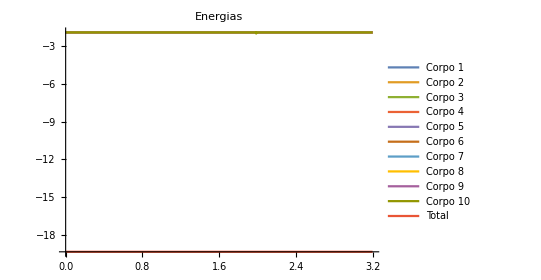

```mathematica
(* Energies for each body and Total *)
Kinetic[t_]=Table[Sum[(inermom[i][j][t])^2,{j,3}]/(2 m[[i]]),{i,n}];
Potential[t_]=Table[-G Sum[If[i≠k,m[[i]]m[[k]]/(2Sqrt[Sum[(inerpos[i][j][t]-inerpos[k][j][t])^2,{j,3}]]),0],{k,n}],{i,n}];
Energy[t_]=Table[{t,Kinetic[t][[i]]+Potential[t][[i]]},{i,n}];
TotalEnergy[t_]={{t,Sum[Energy[t][[i,2]],{i,n}]}};

TotalEnergy[0][[1,2]]
ParametricPlot[Evaluate[Join[Energy[t],TotalEnergy[t]]],{t,0,1*3.197},
PlotRange->All, AspectRatio->0.7,PlotLabel->Style["Energias",FontSize->12],PlotLegends->{"Corpo 1","Corpo 2","Corpo 3","Corpo 4","Corpo 5","Corpo 6","Corpo 7","Corpo 8","Corpo 9","Corpo 10","Total"}]
```

{0,-19.6531}

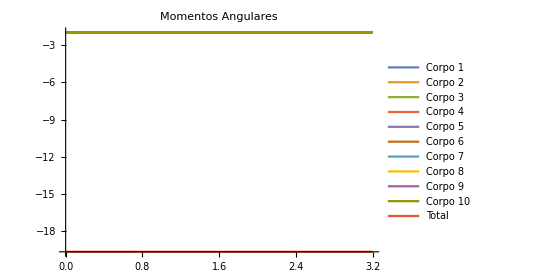

```mathematica
(* Momentum for each body and Total *)
AngMomentum[t_]=Table[{t,Cross[Table[inerpos[i][j][t],{j,3}],Table[inermom[i][j][t],{j,3}]][[3]]},{i,n}];
TotalAngMom[t_]={{t,Sum[AngMomentum[t][[i,2]],{i,n}]}};

TotalAngMom[0][[1]]
ParametricPlot[Evaluate[Join[AngMomentum[t],TotalAngMom[t]]],{t,0,1*3.197},
PlotRange->All,AspectRatio->0.7,PlotLabel->Style["Momentos Angulares",FontSize->12],PlotLegends->{"Corpo 1","Corpo 2","Corpo 3","Corpo 4","Corpo 5","Corpo 6","Corpo 7","Corpo 8","Corpo 9","Corpo 10","Total"}]
```

```mathematica
(* Position and Vel calculus *)
p[1]={0,1};
For[i=2,i≤n,i++,
p[i]=RotationTransform[2Pi/n][p[i-1]];
]
Table[N[p[i],20],{i,n}]
Clear[i]
```

{{0,1.},{-0.58778525229247312917,0.8090169943749474241},{-0.95105651629515357212,0.3090169943749474241},{-0.95105651629515357212,-0.3090169943749474241},{-0.58778525229247312917,-0.8090169943749474241},{0.,-1.},{0.58778525229247312917,-0.8090169943749474241},{0.95105651629515357212,-0.3090169943749474241},{0.95105651629515357212,0.3090169943749474241},{0.58778525229247312917,0.8090169943749474241}}

```mathematica
w=Sqrt[M Sum[1/Sin[j Pi/n],{j,n-1}]/(4n)];

v[1]={w,0};
For[i=2,i≤n,i++,
v[i]=RotationTransform[2Pi/n][v[i-1]];
]
Table[N[v[i],20],{i,n}]
Clear[i]
```

{{1.9653116541584348002,0},{1.5899705274573130641,1.1551812064728532963},{0.607314700378095664,1.8691224552381866682},{-0.607314700378095664,1.8691224552381866682},{-1.5899705274573130641,1.1551812064728532963},{-1.9653116541584348002322693357207163906153887633985911166002940493338,0.},{-1.5899705274573130641,-1.1551812064728532963},{-0.607314700378095664,-1.8691224552381866682},{0.607314700378095664,-1.8691224552381866682},{1.5899705274573130641,-1.1551812064728532963}}